### Functions

barbKappaModAsymp uses α=0

```mathematica
preFactor = 2.680594*^-08;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

### The compactified analytic expression from journal__20180125__limiting_expression_kappa_Barbosa__cylindrical_soln.nb

```mathematica
kapBarbLimvbth[vbth_,kappa_]:=((kappa^(1/2)Gamma[kappa-1/2])/(2 Gamma[kappa])+vbth/(√π(1-3/(2 kappa))^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1(((kappa+((-1+2 kappa) vbth^2)/(1-3/(2 kappa))) Gamma[-1/2+kappa])/(2 √kappa Gamma[kappa])+(2 vbth^3 Hypergeometric2F1[1/2,1+kappa,3/2,-vbth^2/(kappa-3/2)])/(√π (1-3/(2 kappa))^(3/2))-(1/((-1+4 kappa^2) √π)(1+vbth^2/(kappa-3/2))^-kappa ( ((1+2 kappa)vbth)/(1-3/(2 kappa))^(1/2)+(2 kappa^2 (1-3/(2 kappa))^(1/2))/vbth(1- Hypergeometric2F1[1,-1/2-kappa,1/2,-vbth^2/(kappa -3/2)]))))
```

#### The cylindrical-coord version of the Barbosa func, in terms of bulk velocity v_(b,th) = v_b/v_th=√(ΔΦ/(k T)) normalized by the thermal velocity v_th= √(kT/m)(origin: journal__20180125__somesing_work) Integrate with rho^2 Sin[ϕ] as multiplicative factor

```mathematica
(*normFacAlt[vbth_,kappa_]:=2/(π^(1/2)(kappa - 3/2)^(3/2))(1/2 Gamma[kappa-1/2]/Gamma[kappa+1]+vbth/(√π kappa(kappa-3/2)^(1/2))Hypergeometric2F1[1/2,kappa,3/2,-vbth^2/(kappa-3/2)])^-1;
funcAlt[rho_,phi_,vbth_,kappa_,b_]:=(1+(rho^2+vbth^2-2 vbth rho (1 - (Sin[phi])^2 b)^(1/2))/(kappa-3/2 ))^(-(kappa+1))*)
```

```mathematica
(*qMaxF[Ep_,Tm_,kappa_]:=normK[Ep,Tm,kappa] NIntegrate[vperp barbKappaAsymp[vpar,vperp,Ep,Tm,kappa],{vpar,0,∞},{vperp,0,∞}]
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *qMaxF[Ep,Tm,κ]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];*)
```

### Use analytic expression in place of qMaxF

```mathematica
funker[Ep_,Tm_,κ_,Kmeas_]:=Kmeas/preFactor * √Tm *kapBarbLimvbth[vbth[Ep,Tm],κ]*((κ-3/2)^(1/2)Gamma[κ-1/2])/Gamma[κ];
```

### The limiting expression for Barbosa

```mathematica
barbAsymp[deltaPhi_,T_]:=1+2(√(deltaPhi/T))/Erfc[-√(deltaPhi/T)] NIntegrate[Erfc[x],{x,-√(deltaPhi/T),∞}]
```

```mathematica
funkerBarb[Ep_,Tm_,Kmeas_]:=Kmeas/preFactor * √Tm *barbAsymp[Ep,Tm];
```

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
(*for using peak energy*)
Ep = 945;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

## FINALE

```mathematica
kappas={1.55,1.6,1.75,2,2.45,4,10,1000};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 1.55,κ = 1.6,κ = 1.75,κ = 2,κ = κ_t (≃ 2.45),κ = 4,κ = 10,κ = 1000}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

### No labels, handle manually

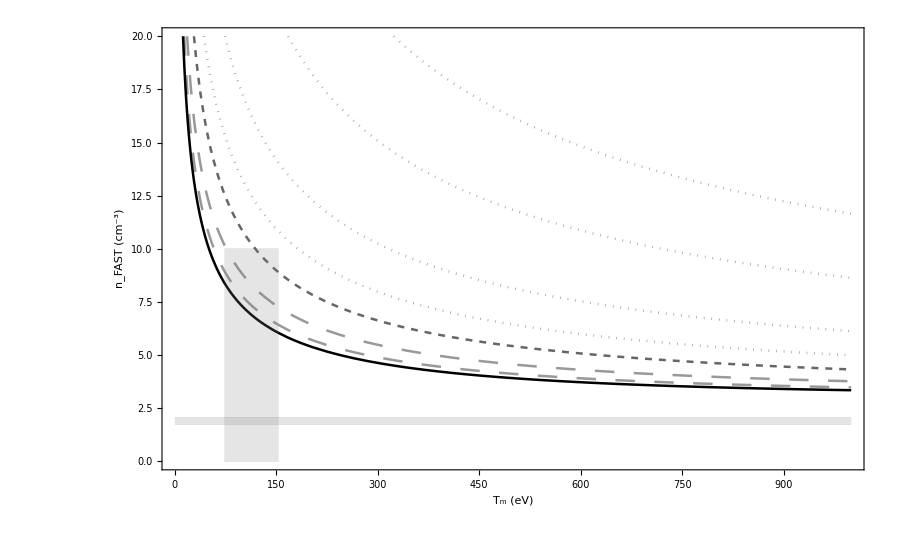

```mathematica
Show[Table[Plot[funker[Ep,Tm,kappas[[k]],measCond],{Tm,1,1000},PlotStyle->styles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,20}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2,3,4,5,6,7,8}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

### No labels, handle manually

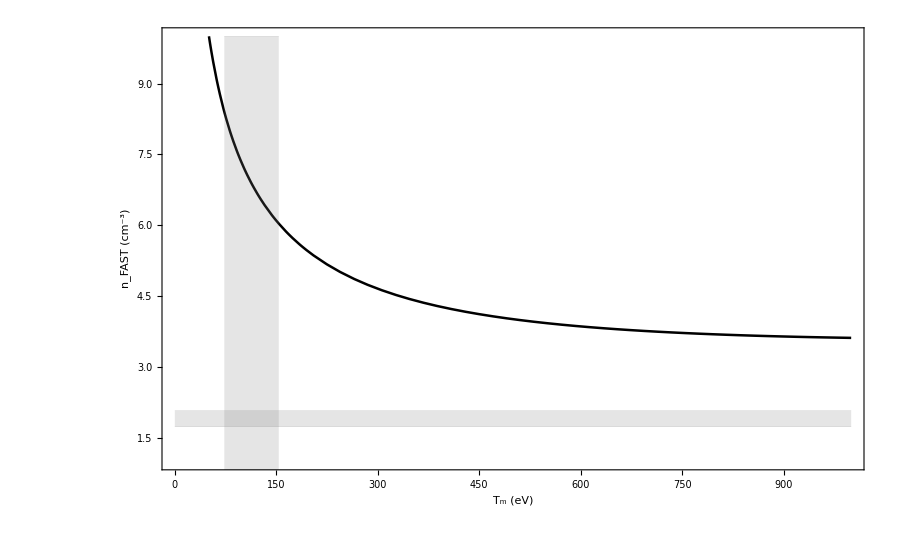

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{1,10}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```